```mathematica
(*En caso de desearse reproducibilidad, puede incluirse un llamado a la función SeedRandom[] de manera que se pueda fijar la semilla pra todos los llamados a funciones pseudoaleatorias y así garantizar exactamente los mismos resultados.*)
```

```mathematica
(*Definimos primero las funciones Ψ y h que serán usadas en adelante.*)
Ψ=Function[{x},Piecewise[{{1,x>0}}],Listable](*Indicadora*);
h=Function[{x1,x2,y1,y2},Ψ[Abs[y1-y2]-Abs[x1-x2]],Listable] (*Definida en el enunciado*);
```

```mathematica
(*Para una sola aplicación de MC, definimos los parametros globales y generamos las muestras.*)
m=5000 (*Tamaño de X*);
n=2000 (*Tamaño de Y*);
M=m+n;
X=RandomVariate[GammaDistribution[1.5,2],m];
Y=RandomVariate[GammaDistribution[1.5,2],n];
```

```mathematica
(*Definimos el número de iteraciones para MC y procedemos a realizar los cálculos.*)
L=2000;
estζ10={};
estζ01={};
pX=X[[1;;Floor[m/2]]];
pY=X[[Ceiling[m/2];;m]] (*Separamos la muestra X en dos partes para calcular las ζ*);
i=1;
While[i<L,
{X1,X2,X3}=RandomSample[pX,3];
{Y1,Y2,Y3,Y4}=RandomSample[pY,4];
AppendTo[estζ10,h[X1,X2,Y1,Y2]h[X1,X3,Y3,Y4]-0.25] (*Bajo Subscript[H, 0], γ = 0.5*);
{X1,X2,X3,X4}=RandomChoice[pX,4];
{Y1,Y2,Y3}=RandomChoice[pY,3];
AppendTo[estζ01,h[X1,X2,Y1,Y2]h[X3,X4,Y1,Y3]-0.25] (*Bajo Subscript[H, 0], γ = 0.5*);
i++;];
ζ10=Mean[estζ10];
ζ01=Mean[estζ01];
λ=m/M;
σ̃=√Abs[(9ζ10)/λ+(16ζ01)/(1-λ)];
```

```mathematica
estU={};
i=1;
While[i<L,
{x1,x2}=RandomSample[X,2];
{y1,y2}=RandomSample[Y,2];
AppendTo[estU,h[x1,x2,y1,y2]];
i++;];
U=Mean[estU];
Ũ=(√M(U-0.5))/(σ̃) (*Bajo Subscript[H, 0], γ = 0.5*)
```

0.62934

```mathematica
(*Definimos una función para realizar todo lo anterior dados m, n, las escalas para las muestras, y el número de iteraciones para MC.*)
MC=Function[{m,n,sX,sY,L},
M=m+n;
X=RandomVariate[GammaDistribution[1.5,sX],m];
Y=RandomVariate[GammaDistribution[1.5,sY],n];
pX=X[[1;;Floor[m/2]]];
pY=X[[Ceiling[m/2];;m]];
estζ10={};
estζ01={};
i=1;
While[i<L,
{X1,X2,X3}=RandomSample[pX,3];
{Y1,Y2,Y3,Y4}=RandomSample[pY,4];
AppendTo[estζ10,h[X1,X2,Y1,Y2]h[X1,X3,Y3,Y4]-0.25];
{X1,X2,X3,X4}=RandomSample[pX,4];
{Y1,Y2,Y3}=RandomSample[pY,3];
AppendTo[estζ01,h[X1,X2,Y1,Y2]h[X3,X4,Y1,Y3]-0.25];
i++];
ζ10=Mean[estζ10];
ζ01=Mean[estζ01];
λ=m/M;
σ̃=√Abs[(9ζ10)/λ+(16ζ01)/(1-λ)];
estU={};
i=1;
While[i<L,
{x1,x2}=RandomSample[X,2];
{y1,y2}=RandomSample[Y,2];
AppendTo[estU,h[x1,x2,y1,y2]];
i++;];
U=Mean[estU];
Ũ=(√M(U-0.5))/(σ̃)];
```

```mathematica
tabUH0=Table[MC[5000,2000,2,2,2000],500] (*Generamos 500 valores bajo Subscript[H, 0] usando la función MC*);
tabUHa=Table[MC[5000,2000,2,3,2000],500] (*Generamos 500 valores bajo Subscript[H, a] usando la función MC*);
```

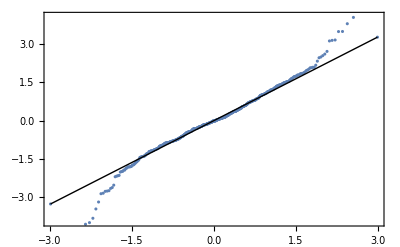

```mathematica
QuantilePlot[tabUH0,NormalDistribution[0,1],ImageSize->Full] (*Generamos el q-q plot para evaluar la normalidad, solo hace falta cambiar el primer argumento para obtener el correspondiente a Subscript[H, 0] o a Subscript[H, a]*)
```

```mathematica
CramerVonMisesTest[tabUH0,NormalDistribution[0,1],"TestConclusion"] (*Realizamos el test de Cramér-von Mises para evaluar la normalidad, solo hace falta cambiar el primer argumento para obtener el correspondiente a Subscript[H, 0] o a Subscript[H, a]*)
```

The null hypothesis that the data is distributed according to the NormalDistribution[0,1] is not rejected at the 5 percent level based on the Cramér-von Mises test.

```mathematica
KolmogorovSmirnovTest[tabUH0,NormalDistribution[0,1],"TestConclusion"](*Realizamos el test de Kolmogorov-Smirnov para evaluar la normalidad, solo hace falta cambiar el primer argumento para obtener el correspondiente a Subscript[H, 0] o a Subscript[H, a]*)
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

The null hypothesis that the data is distributed according to the NormalDistribution[0,1] is not rejected at the 5 percent level based on the Kolmogorov-Smirnov test.

```mathematica
Count[tabUHa,u_/;u>Quantile[NormalDistribution[0,1],0.95]]/500 (*Contamos la proporción de datos que sobrepasan el cuantil del 95% para evaluar la normalidad, solo hace falta cambiar el primer argumento para obtener el correspondiente a Subscript[H, 0] o a Subscript[H, a]*)
```

1